# Cuts in LAB frame

Variables in LAB frame:

```mathematica
p1μ=(E1,0,0,p1);
p2μ=(m,0,0,0);
p3μ=(E3,p3);
p4μ=(E4,p4);
```

Equations (c e=cos θ_e and so forth):

```mathematica
p4 se = p3 sμ
p1=p4 ce + p3 cμ
```

Get avoid of 3 and μ:

```mathematica
cμ=(p1-p4 ce)/p3
p4^2(1-ce^2)=p3^2(1-cμ^2)=p3^2-(p1-p4 ce)^2=p3^2-p1^2-p4^2 ce^2+2 p1 p4 ce
```

```mathematica
p4^2=E4^2-m^2=E3^2-E1^2+2p1 p4 ce
E3^2=(E1+m-E4)^2=E1^2+m^2+E4^2-2E4 E1-2m E4+2m E1
p1 p4 ce=E4 E1+m E4-mE1-m^2
ce=(E4 E1+m E4-mE4-m^2)/(p1 p4)=(E1(E4-m)+m(E4-m))/(√(E1^2-M^2)√(E4^2-m^2))
```

If define (E_4=m+T)

```mathematica
ce=(E1 T+m T)/(√(E1^2-M^2)√(T (2m +T)))
```

this agree with other’s paper.

Calculate the relationship between θ_e and θ_μ, first express θ_μ with θ_e and E4:

```mathematica
p3=p4 se/sμ
p1=p4 ce + (p4 se)/tμ
```

where tμ is tan θ_μ. so

```mathematica
tμ=(p4 se)/(p1-p4 ce)=(√(E4^2-m^2)se)/(√(E1^2-M^2)-√(E4^2-m^2)ce)=(√(T (2m +T))se)/(√(E1^2-M^2)-√(T (2m +T))ce)
```

Then try to eliminate T from ce:

```mathematica
ce=(E1+m)/(√(E1^2-M^2)√((2m +T)/T))
2m=((E1+m)^2/((E1^2-M^2)ce^2)-1)T
T=(2m)/((E1+m)^2/((E1^2-M^2)ce^2)-1)
```

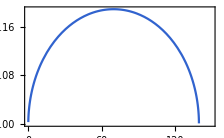
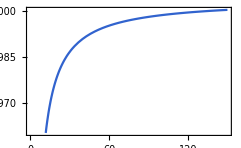
{0.0142684,0.00446262,0.0448804,0.0701909,0.132347,-Graphics-,-Graphics-}

```mathematica
Block[{m=0.000511,M=0.1057,E1=150},
{ce=(E1(E4-m)+m(E4-m))/(√(E1^2-M^2)√(E4^2-m^2));
se=√(1-ce^2);
√(E4^2-m^2)se/.{E4->0.2},
√(E4^2-m^2)se/.{E4->0.02},
√(E4^2-m^2)se/.{E4->2.},
√(E4^2-m^2)se/.{E4->5.},
√(E4^2-m^2)se/.{E4->20.},
Plot[√(E4^2-m^2)se,{E4,0.01,150}],
Plot[ce,{E4,0.2,150}]}
]
```

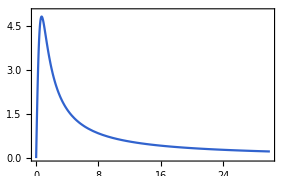

```mathematica
Block[{m=0.000511,M=0.1057,E1=150},
{T[x_]:=(2m)/((E1+m)^2/((E1^2-M^2)Cos[x/1000]^2)-1);
mu[x_]:=1000ArcTan[(√(T[x] (2m +T[x]))Sin[x/1000])/(√(E1^2-M^2)-√(T[x] (2m +T[x]))Cos[x/1000])];
Plot[mu[x],{x,0,30},PlotRange->{{0,30},{0,5}}]
}
]
```